# Data Visuals

## Brendan Apple

```mathematica
DateString[]
```

Sun 7 Jul 2024 17:31:52

### Load Data

#### NICT-2500 Data

```mathematica
nict2500Data = Import["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Data\\priorDatasets\\NICT-2500\\resultsData.json", "Dataset"];
```

#### NICT-1000 Data

```mathematica
nict1000Data = Import["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Data\\priorDatasets\\NICT-1000-1\\resultsData.json", "Dataset"];
```

#### NICT-400 Data

```mathematica
nict400BaseData = Import["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Data\\priorDatasets\\NICT-400\\base\\resultsData.json", "Dataset"];
```

```mathematica
nict400TemperatureData = Import["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Data\\priorDatasets\\NICT-400\\temperatureData.json", "Dataset"];
temperatures = {0.0, 0.2, 0.5, 0.8, 1.0, 1.2, 1.5, 1.8, 2.0};
```

```mathematica
nict400TopPData = Import["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Data\\priorDatasets\\NICT-400\\topPData.json", "Dataset"];
topPs = {0.0, 0.1, 0.2, 0.3, 0.4, 0.5, 0.6, 0.7, 0.8, 0.9, 1.0};
```

### Visualizations

#### NICT-2500 Data

```mathematica
Transpose[nict2500Data]
Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\base\\nict2500ResultsTable.png",Transpose[nict2500Data]]
```

C:\Users\brend\OneDrive\Desktop\School\REX Computational Science 2024\Japanese Translation\Visuals\base\nict2500ResultsTable.png

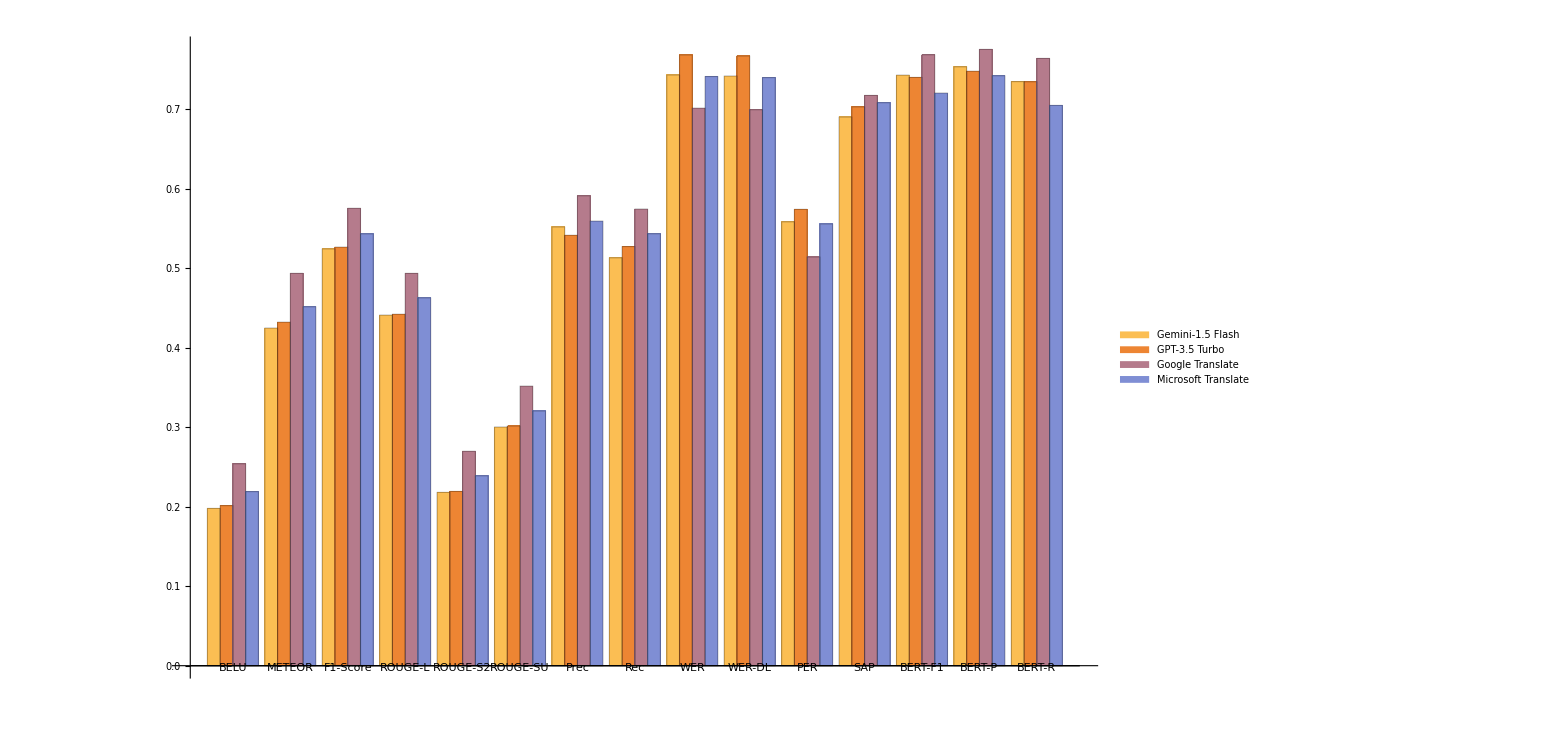

C:\Users\brend\OneDrive\Desktop\School\REX Computational Science 2024\Japanese Translation\Visuals\base\nict2500ResultsGraph.png

```mathematica
nict2500Chart=BarChart[Transpose[nict2500Data],ChartLegends->Automatic,ImageSize->{1200,700}, BarSpacing->{0,0.5},ImagePadding->0,
ChartLabels->{{"BELU","METEOR","F1-Score","ROUGE-L", "ROUGE-S2","ROUGE-SU","Prec", "Rec", "WER","WER-DL","PER","SAP","BERT-F1","BERT-P","BERT-R"},None}]
Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\base\\nict2500ResultsGraph.png",nict2500Chart]
```

#### NICT-1000 Data

```mathematica
Transpose[nict1000Data]
Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\base\\nict1000ResultsTable.png",Transpose[nict1000Data]]
```

C:\Users\brend\OneDrive\Desktop\School\REX Computational Science 2024\Japanese Translation\Visuals\base\nict1000ResultsTable.png

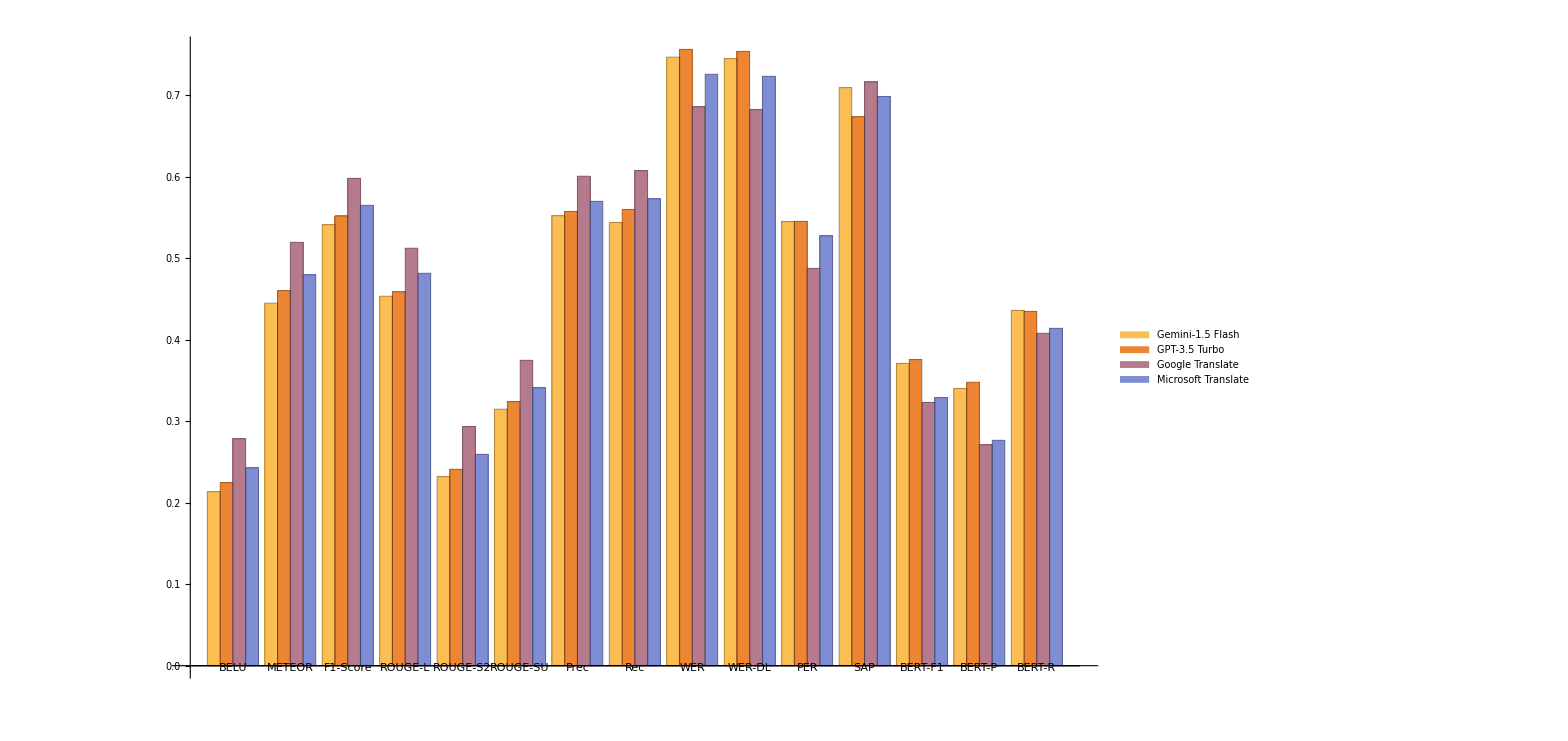

C:\Users\brend\OneDrive\Desktop\School\REX Computational Science 2024\Japanese Translation\Visuals\base\nict1000ResultsGraph.png

```mathematica
nict1000Chart=BarChart[Transpose[nict1000Data],ChartLegends->Automatic,ImageSize->{1200,700}, BarSpacing->{0,0.5},ImagePadding->0,
ChartLabels->{{"BELU","METEOR","F1-Score","ROUGE-L", "ROUGE-S2","ROUGE-SU","Prec", "Rec", "WER","WER-DL","PER","SAP","BERT-F1","BERT-P","BERT-R"},None}]
Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\base\\nict1000ResultsGraph.png",nict1000Chart]
```

#### NICT-400 Data

Base Data

```mathematica
Transpose[nict400BaseData]
```

Temperature Variation

```mathematica
Transpose[nict400TemperatureData]
```

```mathematica
legend=Grid[{
{Graphics[{Blue,Disk[{0,0},0.1]},ImageSize->5],"Gemini-1.5 Flash"},
{Graphics[{Red,Disk[{0,0},0.1]},ImageSize->5],"GPT-3.5 Turbo"},
{Graphics[{Purple,Disk[{0,0},0.1]},ImageSize->5],"Google Translate"},
{Graphics[{Green,Disk[{0,0},0.1]},ImageSize->5],"Microsoft Translate"}
}];
```

FittedModel[…] |     | 0.90855

FittedModel[…] |     | 0.694164

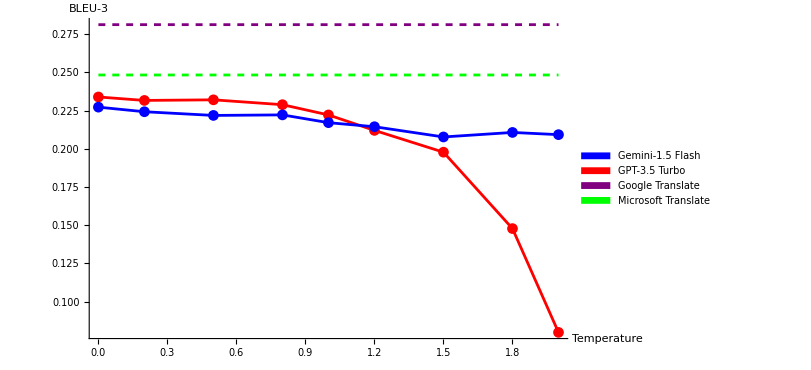

```mathematica
bleuPlot=graphMetric[nict400TemperatureData, temperatures, "BLEU-3"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotBLEU.png", bleuPlot];
```

```mathematica
(*gptTransposition=Transpose@{temperatures,Normal[nict400TemperatureData["GPT-3.5 Turbo", "BLEU-3"]]};
Grid[{{gptRegression=NonlinearModelFit[gptTransposition, a Exp[b x+c]+d, {a,b,c,d}, x], "   ", gptRegression["RSquared"]}}]
Show[bleuPlot, Plot[gptRegression[x],{x, 0.0, 2.0}]]

gptRegression["RSquared"]
Normal[gptRegression]*)
```

FittedModel[…] |     | 0.895713

FittedModel[…] |     | 0.589541

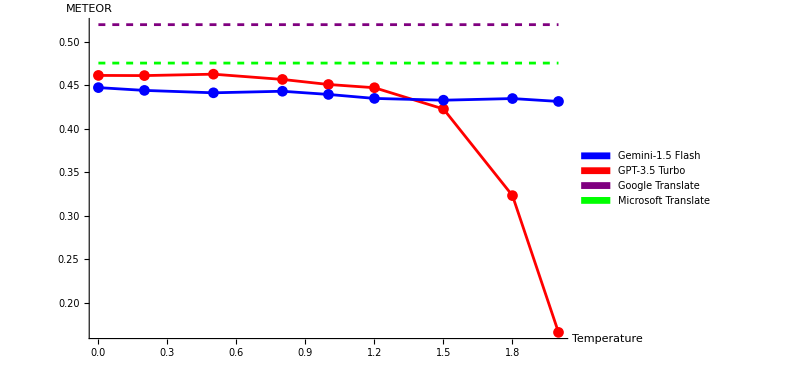

```mathematica
meteorPlot=graphMetric[nict400TemperatureData, temperatures, "METEOR"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotMETEOR.png", meteorPlot];
```

FittedModel[…] |     | 0.850992

FittedModel[…] |     | 0.597551

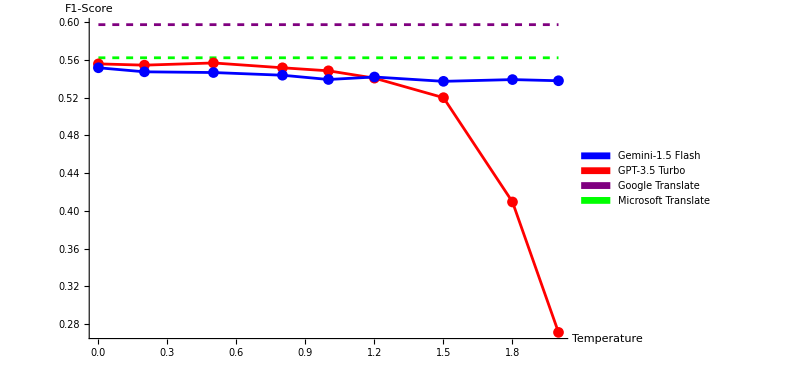

```mathematica
f1Plot=graphMetric[nict400TemperatureData, temperatures, "F1-Score"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotF1-Score.png", f1Plot];
```

FittedModel[…] |     | 0.858334

FittedModel[…] |     | 0.597089

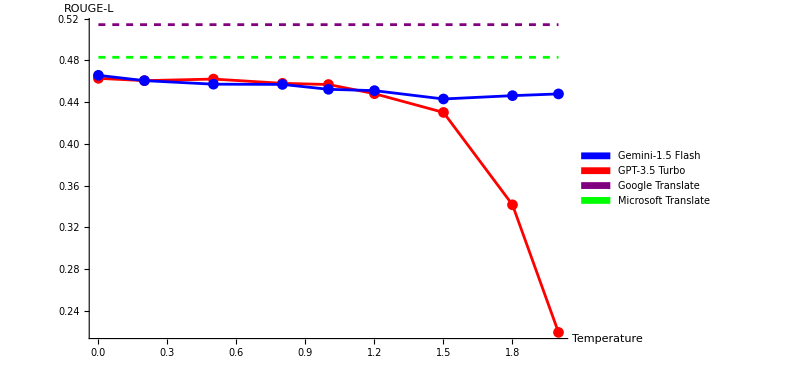

```mathematica
rougeLPlot=graphMetric[nict400TemperatureData, temperatures, "ROUGE-L"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotROUGE-L.png", rougeLPlot];
```

FittedModel[…] |     | 0.849658

FittedModel[…] |     | 0.671277

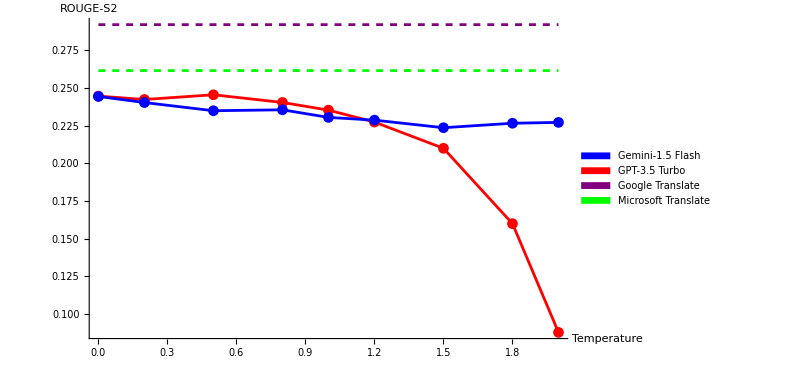

```mathematica
rougeS2Plot=graphMetric[nict400TemperatureData, temperatures, "ROUGE-S2"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotROUGE-S2.png", rougeS2Plot];
```

FittedModel[…] |     | 0.865192

FittedModel[…] |     | 0.642556

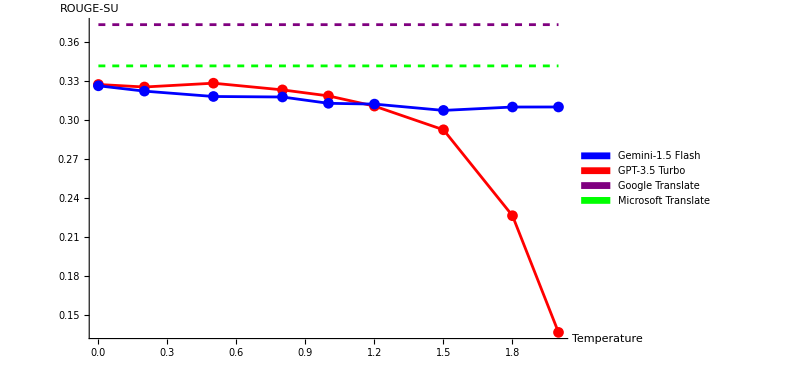

```mathematica
rougeSUPlot=graphMetric[nict400TemperatureData, temperatures, "ROUGE-SU"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotROUGE-SU.png", rougeSUPlot];
```

FittedModel[…] |     | 0.820935

FittedModel[…] |     | 0.597037

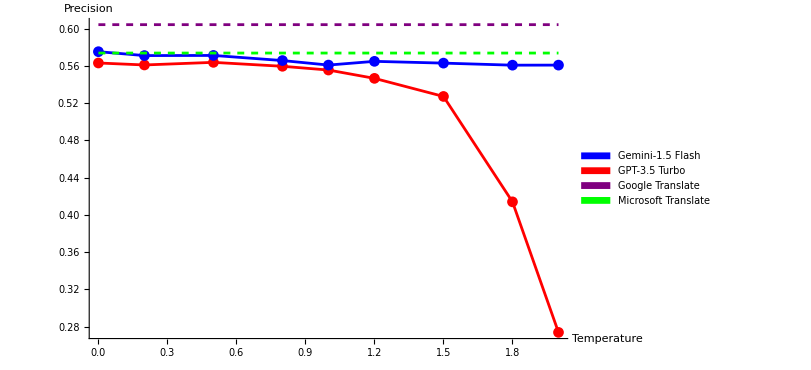

```mathematica
precPlot=graphMetric[nict400TemperatureData, temperatures, "Precision"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotPREC.png", precPlot];
```

FittedModel[…] |     | 0.789855

FittedModel[…] |     | 0.596287

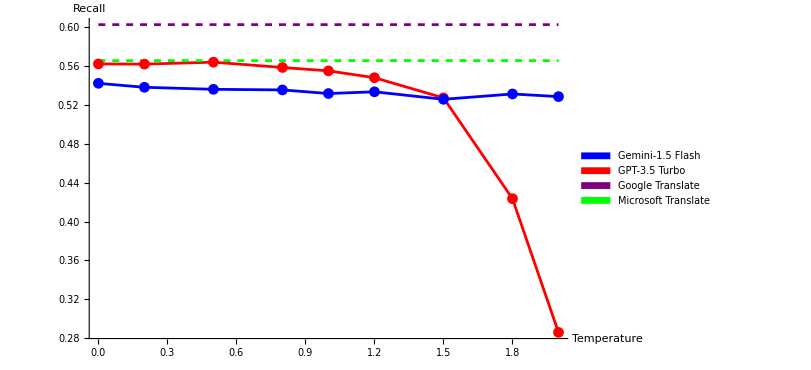

```mathematica
recPlot=graphMetric[nict400TemperatureData, temperatures, "Recall"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotREC.png", recPlot];
```

FittedModel[…] |     | 0.770975

FittedModel[…] |     | 0.622946

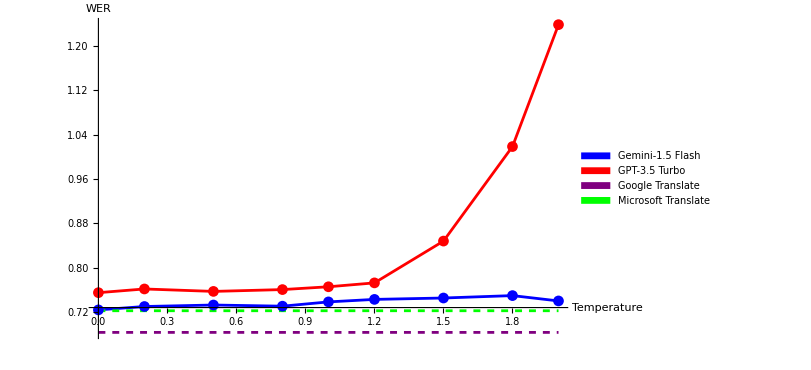

```mathematica
werPlot=graphMetric[nict400TemperatureData, temperatures, "WER"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotWER.png", werPlot];
```

FittedModel[…] |     | 0.999964

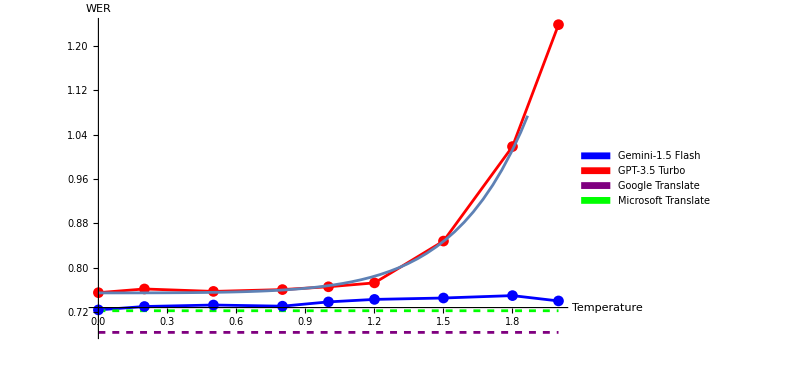

0.999964

0.754524+2.09877×10^-6 ⅇ^(8.7346 √x)

```mathematica
(*gptTransposition=Transpose@{temperatures,Normal[nict400TemperatureData["GPT-3.5 Turbo", "WER"]]};
Grid[{{gptRegression=NonlinearModelFit[gptTransposition, a Exp[b Sqrt[x]]+c, {a,b,c}, x, MaxIterations->Infinity], "   ", gptRegression["RSquared"]}}]
Show[werPlot, Plot[gptRegression[x],{x, 0.0, 2.0}]]

gptRegression["RSquared"]
Normal[gptRegression]*)
```

FittedModel[…] |     | 0.793343

FittedModel[…] |     | 0.623345

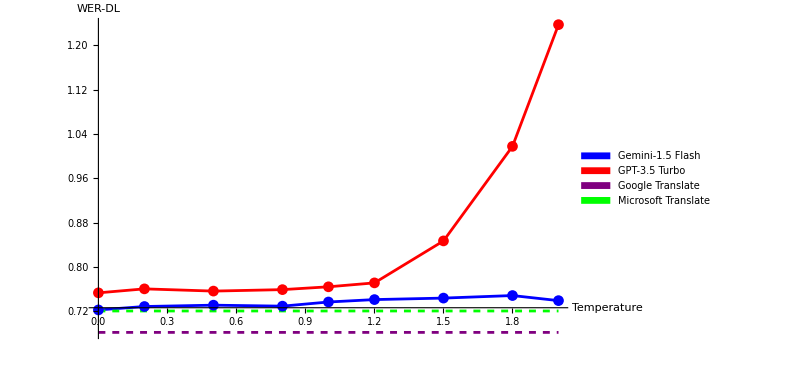

```mathematica
werDLPlot=graphMetric[nict400TemperatureData, temperatures, "WER-DL"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotWER-DL.png", werDLPlot];
```

FittedModel[…] |     | 0.531787

FittedModel[…] |     | 0.6032

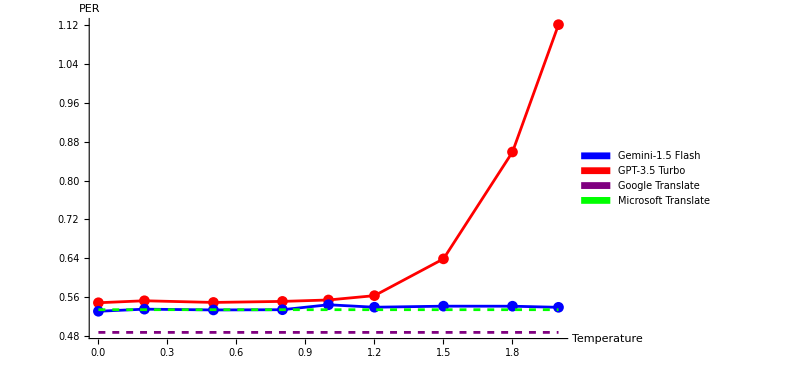

```mathematica
perPlot=graphMetric[nict400TemperatureData, temperatures, "PER"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotPER.png", perPlot];
```

FittedModel[…] |     | 0.0415077

FittedModel[…] |     | 0.51386

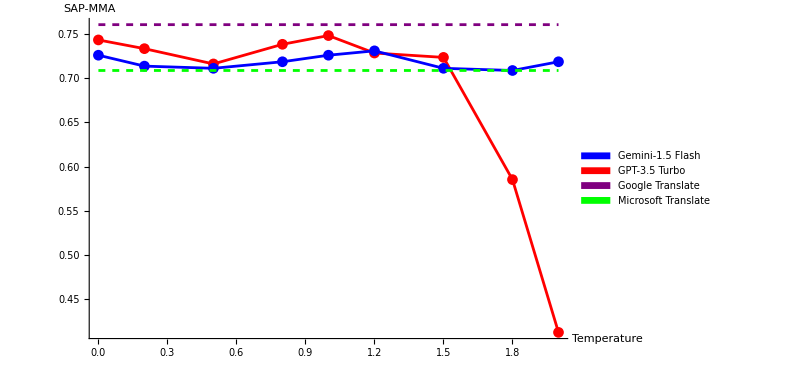

```mathematica
sapPlot=graphMetric[nict400TemperatureData, temperatures, "SAP-MMA"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotSAP-MMA.png", sapPlot];
```

FittedModel[…] |     | 0.0140502

FittedModel[…] |     | 0.489695

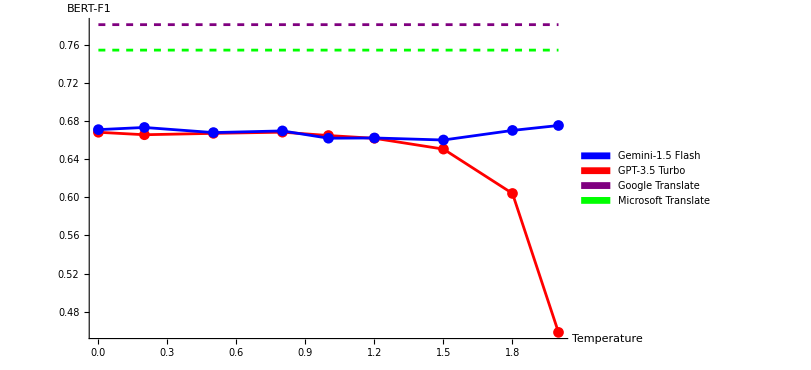

```mathematica
bertf1Plot=graphMetric[nict400TemperatureData, temperatures, "BERT-F1"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotBERT-F1.png", bertf1Plot];
```

FittedModel[…] |     | 0.0202719

FittedModel[…] |     | 0.538125

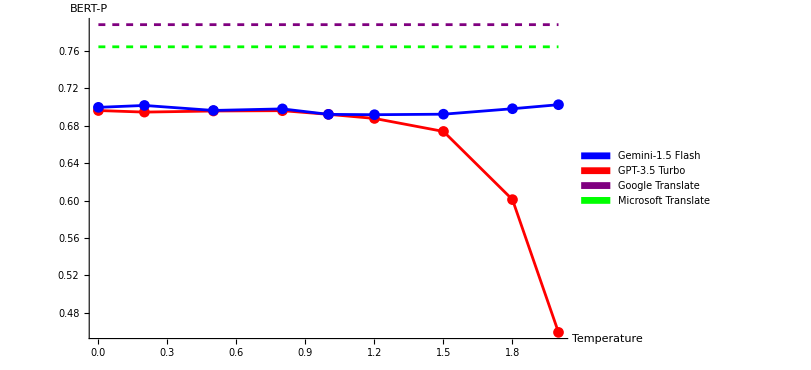

```mathematica
bertpPlot=graphMetric[nict400TemperatureData, temperatures, "BERT-P"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotBERT-P.png", bertpPlot];
```

FittedModel[…] |     | 0.010492

FittedModel[…] |     | 0.435166

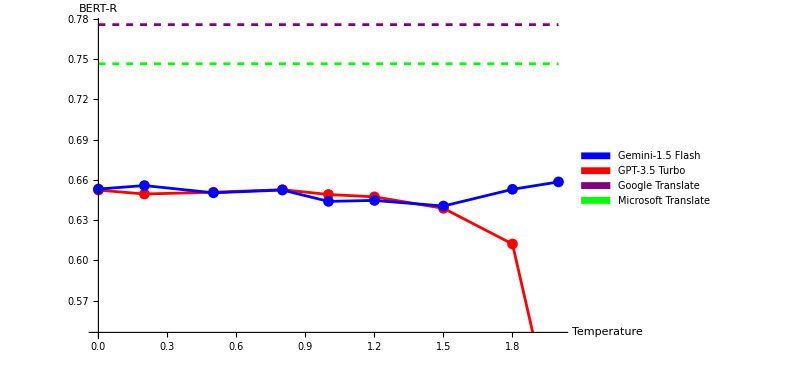

```mathematica
bertrPlot=graphMetric[nict400TemperatureData, temperatures, "BERT-R"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\temperature\\plotBERT-R.png", bertrPlot];
```

Top-P Variation

```mathematica
Transpose[nict400TopPData]
```

FittedModel[…] |     | 0.50202

FittedModel[…] |     | 0.43509

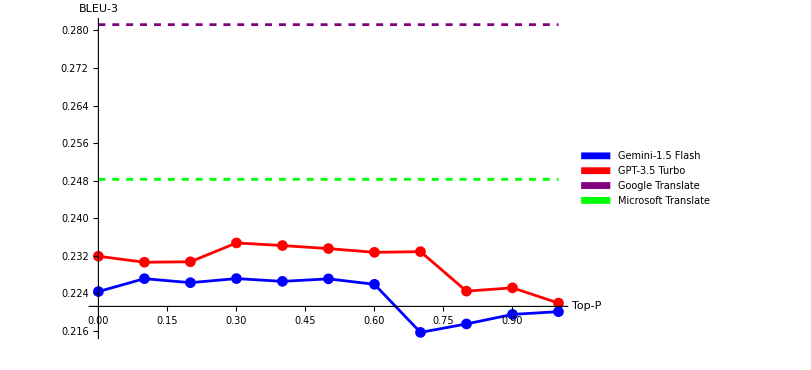

```mathematica
bleuPlot=graphMetric[nict400TopPData, topPs, "BLEU-3"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotBLEU.png", bleuPlot];
```

FittedModel[…] |     | 0.468549

FittedModel[…] |     | 0.278488

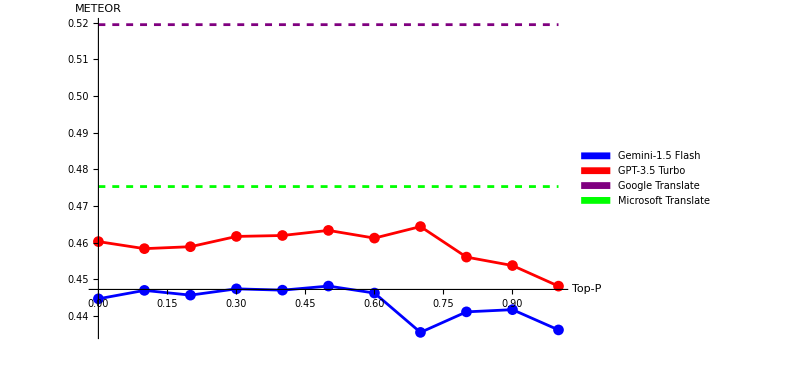

```mathematica
meteorPlot=graphMetric[nict400TopPData, topPs, "METEOR"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotMETEOR.png", meteorPlot];
```

FittedModel[…] |     | 0.513248

FittedModel[…] |     | 0.218109

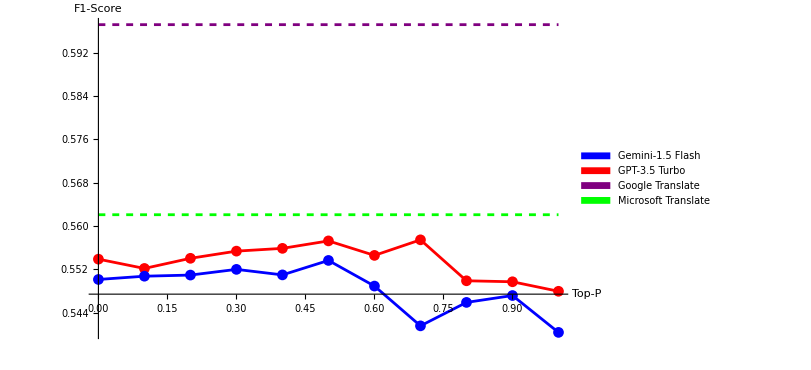

```mathematica
f1Plot=graphMetric[nict400TopPData, topPs, "F1-Score"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotF1-Score.png", f1Plot];
```

FittedModel[…] |     | 0.652737

FittedModel[…] |     | 0.399059

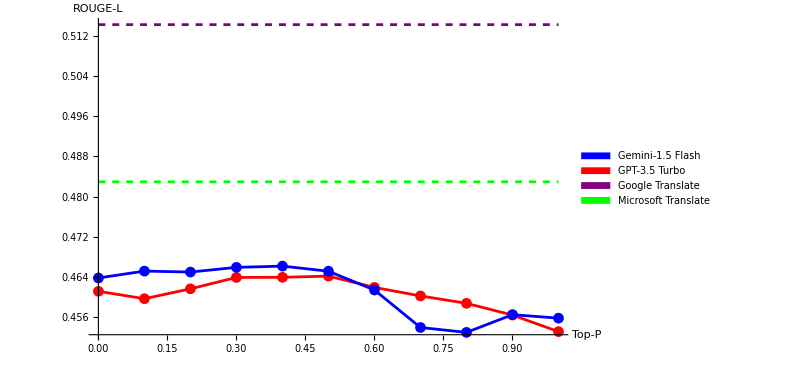

```mathematica
rougeLPlot=graphMetric[nict400TopPData, topPs, "ROUGE-L"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotROUGE-L.png", rougeLPlot];
```

FittedModel[…] |     | 0.657459

FittedModel[…] |     | 0.410341

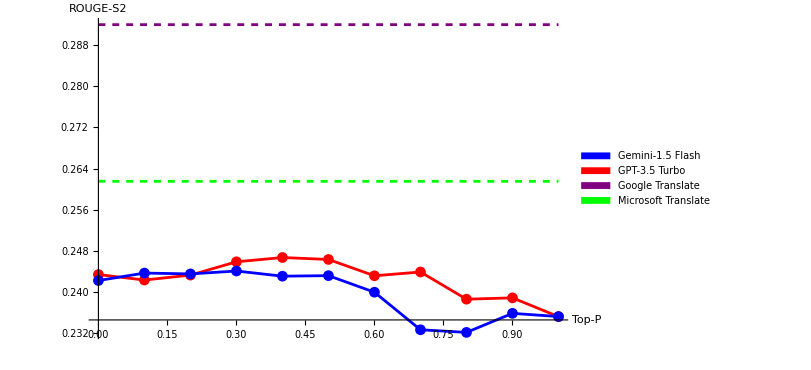

```mathematica
rougeS2Plot=graphMetric[nict400TopPData, topPs, "ROUGE-S2"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotROUGE-S2.png", rougeS2Plot];
```

FittedModel[…] |     | 0.648111

FittedModel[…] |     | 0.367902

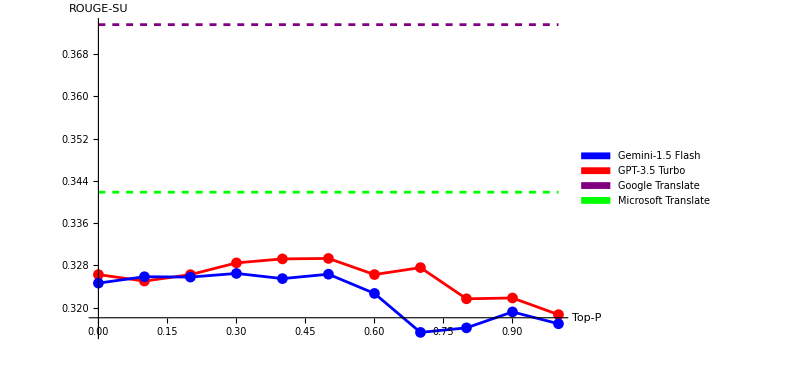

```mathematica
rougeSUPlot=graphMetric[nict400TopPData, topPs, "ROUGE-SU"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotROUGE-SU.png", rougeSUPlot];
```

FittedModel[…] |     | 0.391892

FittedModel[…] |     | 0.116907

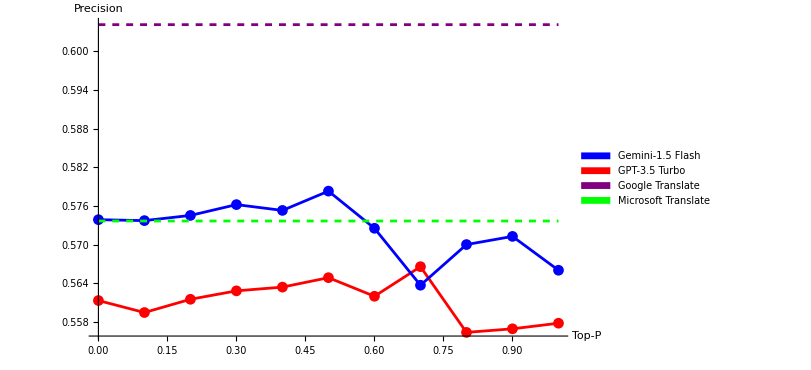

```mathematica
precPlot=graphMetric[nict400TopPData, topPs, "Precision"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotPrecision.png", precPlot];
```

FittedModel[…] |     | 0.598062

FittedModel[…] |     | 0.309591

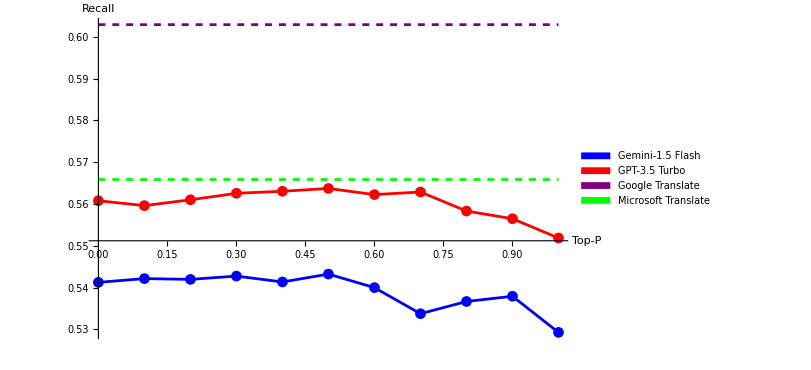

```mathematica
recPlot=graphMetric[nict400TopPData, topPs, "Recall"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotRecall.png", recPlot];
```

FittedModel[…] |     | 0.282282

FittedModel[…] |     | 0.180545

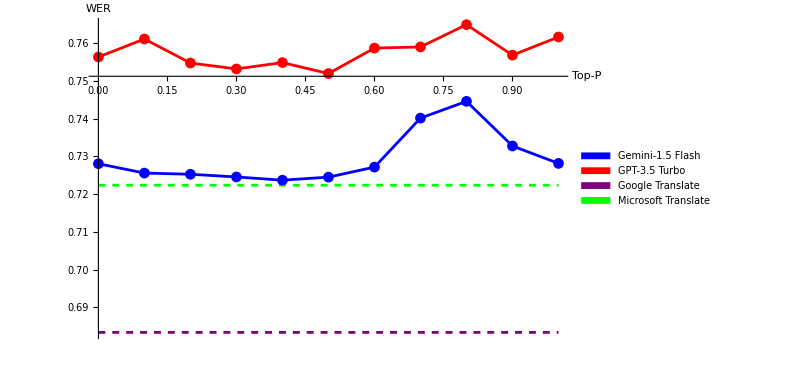

```mathematica
werPlot=graphMetric[nict400TopPData, topPs, "WER"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotWER.png", werPlot];
```

FittedModel[…] |     | 0.277167

FittedModel[…] |     | 0.176913

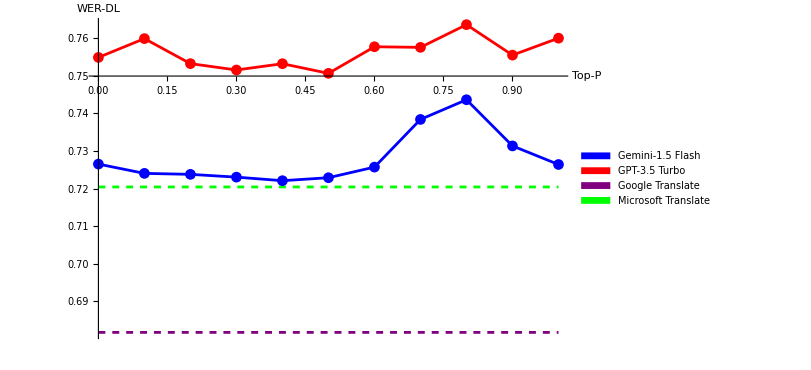

```mathematica
werDLPlot=graphMetric[nict400TopPData, topPs, "WER-DL"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotWER-DL.png", werDLPlot];
```

FittedModel[…] |     | 0.168796

FittedModel[…] |     | 0.00537597

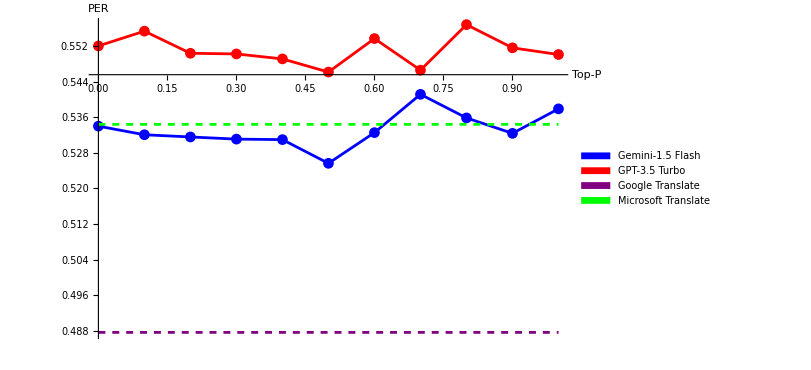

```mathematica
perPlot=graphMetric[nict400TopPData, topPs, "PER"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotPER.png", perPlot];
```

FittedModel[…] |     | 0.000283688

FittedModel[…] |     | 0.126531

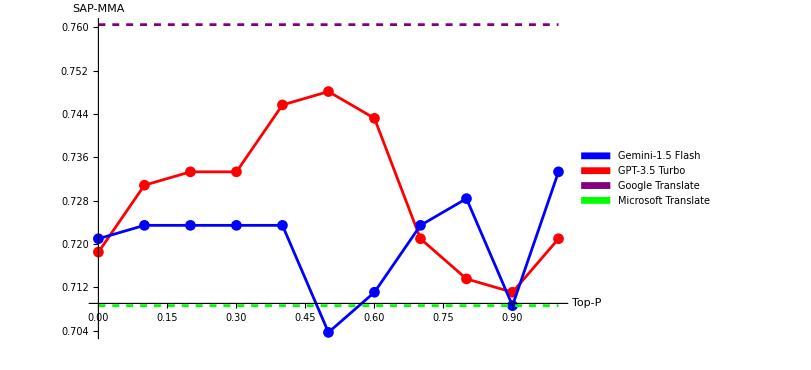

```mathematica
sapPlot=graphMetric[nict400TopPData, topPs, "SAP-MMA"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotSAP-MMA.png", sapPlot];
```

FittedModel[…] |     | 0.156754

FittedModel[…] |     | 0.0248926

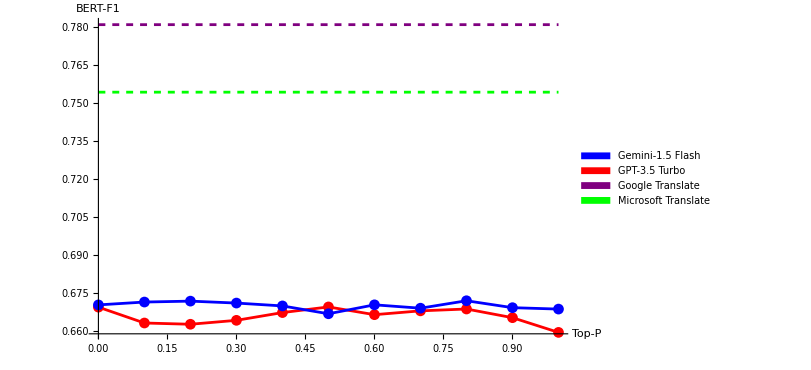

```mathematica
bertf1Plot=graphMetric[nict400TopPData, topPs, "BERT-F1"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotBERT-F1.png", bertf1Plot];
```

FittedModel[…] |     | 0.261312

FittedModel[…] |     | 0.138661

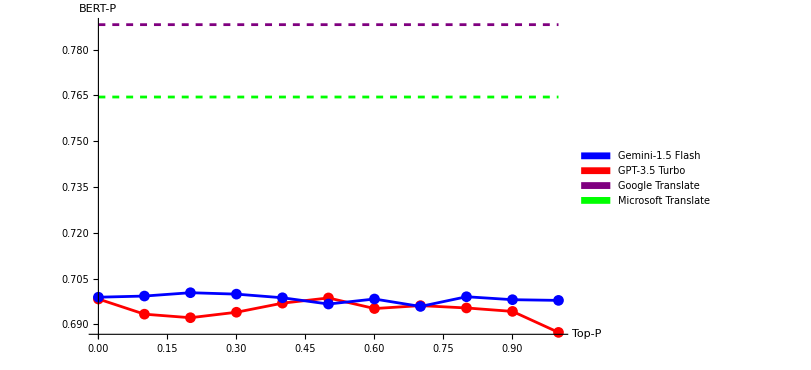

```mathematica
bertpPlot=graphMetric[nict400TopPData, topPs, "BERT-P"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotBERT-P.png", bertpPlot];
```

FittedModel[…] |     | 0.0648141

FittedModel[…] |     | 0.00089531

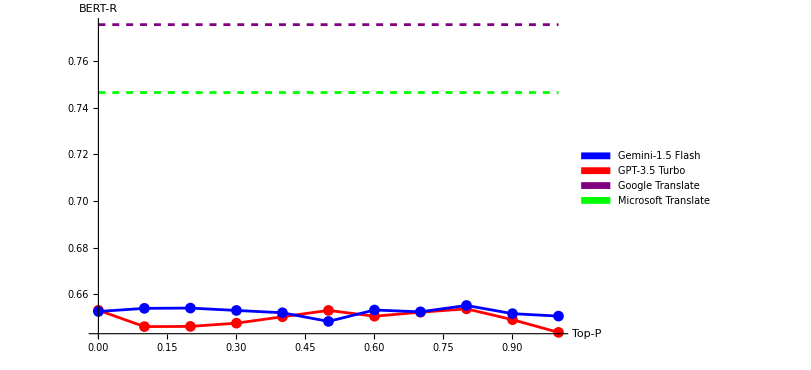

```mathematica
bertrPlot=graphMetric[nict400TopPData, topPs, "BERT-R"]

Export["C:\\Users\\brend\\OneDrive\\Desktop\\School\\REX Computational Science 2024\\Japanese Translation\\Visuals\\top-p\\plotBERT-R.png", bertrPlot];
```

#### Functions

```mathematica
graphMetric[dataset_, xVal_, metric_]:=(
	gemTransposition=Transpose@{xVal, Normal[dataset["Gemini-1.5 Flash", metric]]};
	Print[Grid[{{gemRegression=LinearModelFit[gemTransposition, x,x], "   ", gemRegression["RSquared"]}}]];
	gptTransposition=Transpose@{xVal,Normal[dataset["GPT-3.5 Turbo", metric]]};
	Print[Grid[{{gptRegression=LinearModelFit[gptTransposition, x, x], "   ", gptRegression["RSquared"]}}]];
	
	meteorPlot=Show[
		ListPlot[gptTransposition, AxesLabel->{If[xVal[[Length[xVal]]]==2.0, "Temperature", "Top-P"], metric}, PlotStyle->Red, ImageSize->{600,Automatic}, PlotLegends->legend, Mesh->All, Joined->True], 
		(*Plot[gptRegression[x], {x, 0.0, 2.0}, PlotStyle->Red],*)
		ListPlot[gemTransposition, PlotStyle->Blue, Mesh->All, Joined->True], 
		(*Plot[gemRegression[x], {x, 0.0, 2.0}, PlotStyle->Blue],*)
		Plot[dataset["Google Translate", metric], {x, xVal[[1]], xVal[[Length[xVal]]]}, PlotStyle->{Purple, Dashed}], 
		Plot[dataset["Microsoft Translate", metric], {x, xVal[[1]], xVal[[Length[xVal]]]}, PlotStyle->{Green, Dashed}],
		PlotRange->Automatic
	]
)
```